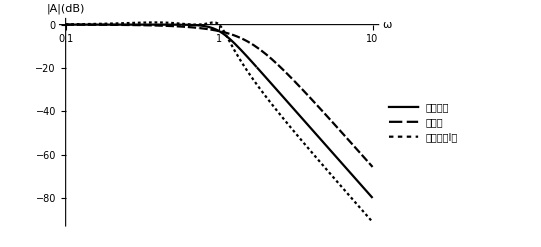

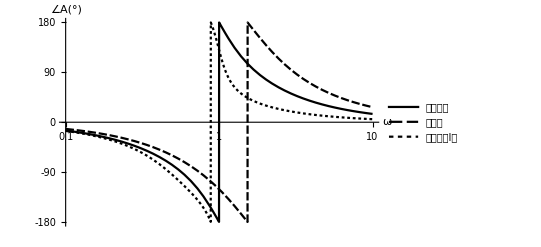

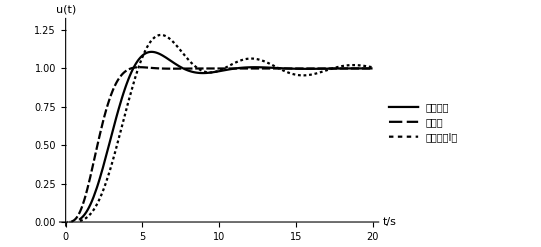

```mathematica
(* butterworth *)
pbut[m_,k_]:=Exp[ⅈ(π/2(1+1/m)+k π/m)];
Hbut[s_,m_]:=1/(∏_(k=0)^(m-1) (s-pbut[m,k]));
(* bessel *)
rbsl[x_,m_]:=((2m-x)!)/(2^(m-x)x!(m-x)!);
Hbslp[s_,m_]:=rbsl[0,m]/(∑_(k=0)^m (rbsl[k,m] s^k));
λbsl=Function[m,λ/.FindRoot[Abs[Hbslp[ⅈ λ,m]]==(√2)/2,{λ,1}]];
(*λbsl2=λbsl[2]*)
Hbsl[s_,m_]:=Hbslp[λbsl[m] s,m];
(* chebyshev *)
pchb[m_,k_,ϵ_]:=-Sinh[1/m ArcSinh[1/ϵ]]Sin[π/2*(2k+1)/m]+ⅈ Cosh[1/m ArcSinh[1/ϵ]]Cos[π/2*(2k+1)/m];
ϵchb[dB_]:=√(10^(0.1*dB)-1);
Hchb[s_,m_,dB_]:=(∏_(k=0)^(m-1) (-pchb[m,k,ϵchb[dB]]))/(∏_(k=0)^(m-1) (s-pchb[m,k,ϵchb[dB]]));
(* ====== *)
dB[a_]:=20*Log10[Abs[a]];
ph[a_]:=180/π*Arg[a];
LogLinearPlot[{dB[Hbut[ⅈ ω,4]],dB[Hbsl[ⅈ ω,4]],dB[Hchb[ⅈ ω,4,1]]},{ω,0.1,10},PlotTheme->"Monochrome",PlotLegends->{"巴特沃斯","贝塞尔","切比雪夫I型"},AxesLabel->{"ω","|A|(dB)"}]
LogLinearPlot[{ph[Hbut[ⅈ ω,4]],ph[Hbsl[ⅈ ω,4]],ph[Hchb[ⅈ ω,4,1]]},{ω,0.1,10},PlotTheme->"Monochrome",Exclusions->None,PlotLegends->{"巴特沃斯","贝塞尔","切比雪夫I型"},PlotRange->{-180,180},Ticks->{Automatic,Table[-180+k*45,{k,0,8}]},AxesLabel->{"ω","∠A(°)"}]
TRbut=InverseLaplaceTransform[Hbut[s,4]/s,s,t];
TRbsl=InverseLaplaceTransform[Hbsl[s,4]/s,s,t];
TRchb=InverseLaplaceTransform[Hchb[s,4,1]/s,s,t];
Plot[{TRbut,TRbsl,TRchb},{t,0,20},PlotTheme->"Monochrome",PlotRange->{0,1.3},PlotLegends->{"巴特沃斯","贝塞尔","切比雪夫I型"},AxesLabel->{"t/s","u(t)"}]
```